# Local Taylor Approximations to Toy Nonlocal Potentials

```mathematica
Clear[λ1,λ2,b,n1,l1,ml1,n,l,ml,m]
$Assumptions=λ1>0&&λ2>0&&b>0&&r≥0&&rprime≥0&&r1≥0&&r2≥0&&x1≥0&&x2≥0&&y1≥0&&y2≥0&&z1≥0&&z2≥0;
Off[ClebschGordan::phy];
Off[ClebschGordan::tri];
```

```mathematica
(* Load Vegas Monte Carlo integration routine from Cuba-4.2 *)
SetDirectory["/Users/coryschillaci/Desktop/Cuba-4.2/"];
link=Install["Vegas"]
On[Vegas::success];
Nσ=6; (* Range of integrals in terms of λ1,λ2 *)
```

LinkObject[…]

```mathematica
(*Harmonic oscillator radial wavefunctions with n=0,1,2,...*)
R[n_,l_,r_]:=Sqrt[(2Gamma[n+1])/(b^3 Gamma[n+l+3/2])](r/b)^l Exp[-r^2/(2 b^2)]LaguerreL[n,l+1/2,r^2/b^2];
```

## In this section, evaluate the matrix elements of the local approximation to a nonlocal Gaussian potential

```mathematica
(* Gaussian in Subscript[r, 1], Subscript[r, 2] cartesian coordinates. Include prefactor so that limit as λ2->0 
gives a delta function.

Note that it is already symmetric under r <-> rprime. *)
Vx1x2[x1_,y1_,z1_,x2_,y2_,z2_]:=1/(π^3 λ1^3 λ2^3)Exp[-2(x1^2+y1^2+z1^2)/λ1^2]Exp[-(x2^2+y2^2+z2^2)/(2 λ2^2)]
```

```mathematica
(* The delta function limit, which should be reproduced exactly. Expressed in r1 coordinate after r2 integration *)
VLimit[r1_]:=2^(3/2)/(π^(3/2)λ1^3)Exp[-2 r1^2/λ1^2]
VLimit[n1_,l1_,ml1_,n_,l_,ml_]:=If[l1==l&&ml1==ml,Integrate[R[n1,l1,r]VLimit[r]R[n,l,r] r^2,{r,0,∞}],0]
```

```mathematica
(* These are the full nonlocal matrix elements, evaluated numerically *)
Integrand[n1_,l1_,ml1_,n_,l_,ml_]:=Integrand[n1,l1,ml1,n,l,ml]=If[l==0&&l1==0,Simplify[1/(4π)R[n1,0,Sqrt[(x1-x2/2)^2+(y1-y2/2)^2+(z1-z2/2)^2]]R[n,0,Sqrt[(x1+x2/2)^2+(y1+y2/2)^2+(z1+z2/2)^2]]Vx1x2[x1,y1,z1,x2,y2,z2]], Simplify[R[n1,l,Sqrt[(x1-x2/2)^2+(y1-y2/2)^2+(z1-z2/2)^2]]SphericalHarmonicY[l1,ml1,ArcCos[(z1-z2/2)/Sqrt[(x1-x2/2)^2+(y1-y2/2)^2+(z1-z2/2)^2]],ArcTan[(y1-y2/2)/(x1-x2/2)]]R[n,l,Sqrt[(x1+x2/2)^2+(y1+y2/2)^2+(z1+z2/2)^2]]SphericalHarmonicY[l1,ml1,ArcCos[(z1+z2/2)/Sqrt[(x1+x2/2)^2+(y1+y2/2)^2+(z1+z2/2)^2]],ArcTan[(y1+y2/2)/(x1+x2/2)]]Vx1x2[x1,y1,z1,x2,y2,z2]]]
VNonLocal[n1_,l1_,ml1_,n_,l_,ml_]:=If[ml1==ml&&l==l1,Vegas[Integrand[n1,l1,ml1,n,l,ml],{x1,-Nσ  λ1,Nσ λ1},{y1,-Nσ λ1,Nσ λ1},{z1,-Nσ λ1,Nσ λ1},{x2,-Nσ  λ2,Nσ  λ2},{y2,-Nσ  λ2,Nσ  λ2},{z2,-Nσ  λ2,Nσ  λ2},MaxPoints->10^7,Verbose->0],0]
```

```mathematica
Clear[λ1,λ2,b]
Integrand[2,0,0,2,0,0]
λ1=1;λ2=.01;b=1;
Vegas[Integrand[2,0,0,2,0,0],{x1,-Nσ  λ1,Nσ λ1},{y1,-Nσ λ1,Nσ λ1},{z1,-Nσ λ1,Nσ λ1},{x2,-Nσ  λ2,Nσ  λ2},{y2,-Nσ  λ2,Nσ  λ2},{z2,-Nσ  λ2,Nσ  λ2},MaxPoints->10^6,Verbose->1]
VLimit[2,0,0,2,0,0]//N
Clear[λ1,λ2,b]
```

1/(1920 b^11 π^(9/2) λ1^3 λ2^3)ⅇ^(-((4 x1^2+x2^2+4 y1^2+y2^2+4 z1^2+z2^2) λ1^2 λ2^2+2 b^2 (x2^2 λ1^2+y2^2 λ1^2+z2^2 λ1^2+4 x1^2 λ2^2+4 y1^2 λ2^2+4 z1^2 λ2^2))/(4 b^2 λ1^2 λ2^2)) (60 b^4-20 b^2 (4 x1^2-4 x1 x2+x2^2+4 y1^2-4 y1 y2+y2^2+4 z1^2-4 z1 z2+z2^2)+(4 x1^2-4 x1 x2+x2^2+4 y1^2-4 y1 y2+y2^2+4 z1^2-4 z1 z2+z2^2)^2) (60 b^4-20 b^2 (4 x1^2+4 x1 x2+x2^2+4 y1^2+4 y1 y2+y2^2+4 z1^2+4 z1 z2+z2^2)+(4 x1^2+4 x1 x2+x2^2+4 y1^2+4 y1 y2+y2^2+4 z1^2+4 z1 z2+z2^2)^2)

Iteration 1:  1000 integrand evaluations so far
[1] 32.4292 +- 32.4276  	chisq 0 (0 df)

Iteration 2:  2500 integrand evaluations so far
[1] 0.0292905 +- 0.019907  	chisq 0.998296 (1 df)

Iteration 3:  4500 integrand evaluations so far
[1] 0.0347226 +- 0.0109776  	chisq 1.10529 (2 df)

Iteration 4:  7000 integrand evaluations so far
[1] 0.045816 +- 0.00701598  	chisq 2.83168 (3 df)

Iteration 5:  10000 integrand evaluations so far
[1] 0.0536884 +- 0.00480955  	chisq 5.20692 (4 df)

Iteration 6:  13500 integrand evaluations so far
[1] 0.059548 +- 0.00255138  	chisq 7.27248 (5 df)

Iteration 7:  17500 integrand evaluations so far
[1] 0.0599708 +- 0.00118121  	chisq 7.30745 (6 df)

Iteration 8:  22000 integrand evaluations so far
[1] 0.0603842 +- 0.000817558  	chisq 7.54248 (7 df)

Iteration 9:  27000 integrand evaluations so far
[1] 0.0607421 +- 0.000756499  	chisq 8.87558 (8 df)

Iteration 10:  32500 integrand evaluations so far
[1] 0.0606431 +- 0.000596264  	chisq 8.92083 (9 df)

Iteration 11:  38500 integrand evaluations so far
[1] 0.060855 +- 0.00050871  	chisq 9.3853 (10 df)

Iteration 12:  45000 integrand evaluations so far
[1] 0.0609356 +- 0.000397727  	chisq 9.44978 (11 df)

Iteration 13:  52000 integrand evaluations so far
[1] 0.0610937 +- 0.000313619  	chisq 9.8676 (12 df)

Iteration 14:  59500 integrand evaluations so far
[1] 0.0612174 +- 0.000295049  	chisq 11.2209 (13 df)

Iteration 15:  67500 integrand evaluations so far
[1] 0.0613194 +- 0.00026579  	chisq 11.8549 (14 df)

Iteration 16:  76000 integrand evaluations so far
[1] 0.0613266 +- 0.000224993  	chisq 11.8575 (15 df)

Iteration 17:  85000 integrand evaluations so far
[1] 0.0613679 +- 0.000190544  	chisq 11.9767 (16 df)

Iteration 18:  94500 integrand evaluations so far
[1] 0.0614031 +- 0.000175385  	chisq 12.1994 (17 df)

Iteration 19:  104500 integrand evaluations so far
[1] 0.0614673 +- 0.000164243  	chisq 13.2898 (18 df)

Iteration 20:  115000 integrand evaluations so far
[1] 0.061474 +- 0.000151564  	chisq 13.3011 (19 df)

Iteration 21:  126000 integrand evaluations so far
[1] 0.0614542 +- 0.000137369  	chisq 13.3974 (20 df)

Iteration 22:  137500 integrand evaluations so far
[1] 0.0614243 +- 0.000126665  	chisq 13.7134 (21 df)

Iteration 23:  149500 integrand evaluations so far
[1] 0.0614037 +- 0.000117699  	chisq 13.9063 (22 df)

Iteration 24:  162000 integrand evaluations so far
[1] 0.0614232 +- 0.000111518  	chisq 14.1749 (23 df)

Iteration 25:  175000 integrand evaluations so far
[1] 0.0614403 +- 0.000105294  	chisq 14.3903 (24 df)

Iteration 26:  188500 integrand evaluations so far
[1] 0.0614349 +- 9.91709e-05  	chisq 14.4132 (25 df)

Iteration 27:  202500 integrand evaluations so far
[1] 0.0614387 +- 9.36504e-05  	chisq 14.4265 (26 df)

Iteration 28:  217000 integrand evaluations so far
[1] 0.0614451 +- 8.93902e-05  	chisq 14.4795 (27 df)

Iteration 29:  232000 integrand evaluations so far
[1] 0.0614421 +- 8.56049e-05  	chisq 14.4928 (28 df)

Iteration 30:  247500 integrand evaluations so far
[1] 0.0614521 +- 8.23968e-05  	chisq 14.6767 (29 df)

Iteration 31:  263500 integrand evaluations so far
[1] 0.0614645 +- 7.92019e-05  	chisq 14.9756 (30 df)

Iteration 32:  280000 integrand evaluations so far
[1] 0.0614624 +- 7.5946e-05  	chisq 14.9848 (31 df)

Iteration 33:  297000 integrand evaluations so far
[1] 0.0614665 +- 7.31649e-05  	chisq 15.0267 (32 df)

Iteration 34:  314500 integrand evaluations so far
[1] 0.0614712 +- 7.04751e-05  	chisq 15.0834 (33 df)

Iteration 35:  332500 integrand evaluations so far
[1] 0.0614823 +- 6.83625e-05  	chisq 15.5037 (34 df)

Iteration 36:  351000 integrand evaluations so far
[1] 0.0614844 +- 6.635e-05  	chisq 15.5204 (35 df)

Iteration 37:  370000 integrand evaluations so far
[1] 0.0614939 +- 6.48374e-05  	chisq 15.9716 (36 df)

Iteration 38:  389500 integrand evaluations so far
[1] 0.0614962 +- 6.29586e-05  	chisq 15.994 (37 df)

Iteration 39:  409500 integrand evaluations so far
[1] 0.0614923 +- 6.09585e-05  	chisq 16.0547 (38 df)

Vegas::success: Needed 409500 function evaluations.

{{0.0614923,0.0000609585,0.000676638}}

0.0615493

```mathematica
(* Try evaluating for one set of λ1, λ2, b.
 Note that the integration gives lots of warnings. *) 
Integrand[0,1,0,0,1,0]
λ1=1;λ2=1;b=1;
VNonLocal[0,1,0,0,1,0]
Clear[λ1,λ2,b]
```

(ⅇ^(-((4 x1^2+x2^2+4 y1^2+y2^2+4 z1^2+z2^2) λ1^2 λ2^2+2 b^2 (x2^2 λ1^2+y2^2 λ1^2+z2^2 λ1^2+4 x1^2 λ2^2+4 y1^2 λ2^2+4 z1^2 λ2^2))/(4 b^2 λ1^2 λ2^2)) (4 z1^2-z2^2))/(2 b^5 π^(9/2) λ1^3 λ2^3)

Vegas::accuracy: Desired accuracy was not reached within 10049500 function evaluations.

{{8.88799×10^-7,8.95921×10^-6,0.}}

```mathematica
(* This is the Gaussian potential in spherical coordinates. Note that it is not manifestly symmetric in r1, r2. *)
V[r1_,r2_]:=1/(π^3 λ1^3 λ2^3)Exp[-2 r1^2/λ1^2]Exp[-r2^2/(2 λ2^2)];
```

```mathematica
(* Plot the potential in the new coordinates *)
Plot3D[ReplaceAll[V[r1,r2],{λ1->1,λ2->2}],{r1,0,10},{r2,0,10},PlotRange->All]
```

-Graphics3D-

```mathematica
(* These are the moments of the potential necessary to calculate the local Taylor approximation *)
V0[r1_]:=4π Integrate[V[r1,r2] r2^2,{r2,0,∞}]
V2[r1_]:=Integrate[V[r1,r2] r2^4,{r2,0,∞}]
```

```mathematica
(* Since they can be calculated analytically, take a look at V0 and V2 *)
V0[r1]
V2[r1]
```

(2 √2 ⅇ^(-(2 r1^2)/λ1^2))/(π^(3/2) λ1^3)

(3 ⅇ^(-(2 r1^2)/λ1^2) λ2^2)/(√2 π^(5/2) λ1^3)

```mathematica
(* Matrix elements (NOT REDUCED) of the gradient and laplacian, 
   needed to calculate the Taylor approximation *)
gradME[n1_,l1_,ml1_,n_,l_,ml_,m_]:=If[Abs[l-l1]≤1&&ml1==ml+m,-1/b(-1)^(l1-ml1)ThreeJSymbol[{l1,ml1},{1,m},{l,ml}](KroneckerDelta[l1,l+1]Sqrt[l+1](Sqrt[n+l+3/2]KroneckerDelta[n1,n]+Sqrt[n]KroneckerDelta[n1,n-1])+KroneckerDelta[l1,l-1]Sqrt[l](Sqrt[n+l+1/2]KroneckerDelta[n1,n]+Sqrt[n+1]KroneckerDelta[n1,n+1])),0]
laplacianME[n1_,l1_,ml1_,n_,l_,ml_]:=If[Abs[n-n1]≤1&&l1==l&&ml1=ml,-1/b^2 Sqrt[2l+1]KroneckerDelta[l1,l]KroneckerDelta[ml1,ml](KroneckerDelta[n1,n+1]Sqrt[(n+1)(n+l+3/2)]+KroneckerDelta[n1,n](2n+l+3/2)+KroneckerDelta[n1,n-1]Sqrt[n(n+l+1/2)]),0]
```

```mathematica
(* This is the local Taylor approximation to the nonlocal potential when it is spherically symmetric in r1, r2 *)
VLocal[n1_,l1_,ml1_,n_,l_,ml_]:=If[l1==l&&ml1==ml,Integrate[r^2 R[n1,l1,r]R[n,l,r]V0[r],{r,0,∞}],0]+
If[l1==l&&ml1==ml,π/6 Sum[laplacianME[n1,l1,ml1,n2,l1,ml1]Integrate[r^2 R[n2,l1,r]R[n,l,r]V2[r],{r,0,∞}],{n2,Max[n1-1,0],n1+1}]+π/6 Sum[ Integrate[r^2 R[n1,l1,r]R[n2,l1,r]V2[r],{r,0,∞}]laplacianME[n2,l,ml,n,l,ml],{n2,Max[n-1,0],n+1}]-π/3 Sum[(-1)^m gradME[n1,l1,ml1,n2,l2,ml1+m,-m]Integrate[r^2 R[n2,l2,r]R[n3,l2,r]V2[r],{r,0,∞}]gradME[n3,l2,ml+m,n,l,ml,m],{l2,l1-1,l1+1},{n2,Max[n1-1,0],n1+1},{n3,Max[n-1,0],n+1},{m,-1,1}],0]
```

```mathematica
(* Look at one matrix element for sanity check *)
VLocal[0,0,0,0,0,0]/.{λ1->λ11 b,λ2->λ22 b}//FullSimplify
VLocal[2,0,0,2,0,0]/.{λ1->λ11 b,λ2->λ22 b}//FullSimplify
```

(4 (2+λ11^2)-(6+λ11^2) λ22^2)/(√2 b^3 π^(3/2) (2+λ11^2)^(5/2))

(12 (2+λ11^2) (30+20 λ11^4+λ11^8)-(1980+250 λ11^2+1280 λ11^4+268 λ11^6+90 λ11^8+11 λ11^10) λ22^2)/(3 √2 b^3 π^(3/2) (2+λ11^2)^(13/2))

#### Plot matrix elements of the local and nonlocal potentials together

```mathematica
(* Make a table for <0 0 0| V | 0 0 0> with fixed λ1 and varying λ2
 to see numerical comparison and get an idea of integration error *)
Off[General::stop]
n1=0;n=0;
l1=0;l=0;
ml1=0;ml=0;
Integrand[n1,l1,ml1,n,l,ml];
λ1=1;b=1;
VLimit[n1,l1,ml1,n,l,ml]//N
Table[N[{VNonLocal[n1,l1,ml1,n,l,ml][[1,1]],VLocal[n1,l1,ml1,n,l,ml]}],{λ2,.05,.6,.25}]
Clear[n1,n,l1,l,ml1,ml,λ1,λ2,b]
On[General::stop]
```

0.0977548

Vegas::success: Needed 188500 function evaluations.

Vegas::success: Needed 202500 function evaluations.

{{0.0975701,0.0976123},{0.0915155,0.0926227},{0.0791048,0.0805052}}

Vegas::success: Needed 202500 function evaluations.

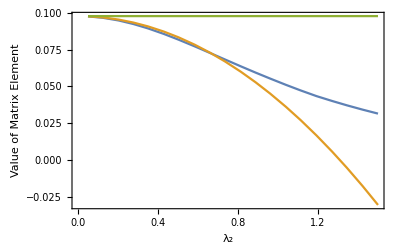

```mathematica
(* Plot <0 0 0| V | 0 0 0> with fixed λ1=1 and varying λ2
Blue is exact, orange is Taylor approximation *)
n1=0;n=0;
l1=0;l=0;
ml1=0;ml=0;
Integrand[n1,l1,ml1,n,l,ml]; (* Initialize integrand if necessary*)
λ1=1;b=1;
λ2min=.05;
λ2max=1.5;
Monitor[Plot[{VNonLocal[n1,l1,ml1,n,l,ml][[1,1]],VLocal[n1,l1,ml1,n,l,ml],VLimit[n1,l1,ml1,n,l,ml]},{λ2,λ2min,λ2max},PlotPoints->20,MaxRecursion->0,PlotRange->{{0,λ2max},All},Frame->True,FrameLabel->{"λ_2","Value of Matrix Element"}],ProgressIndicator[λ2,{λ2min,λ2max}]]
Clear[n1,n,l1,l,ml1,ml,λ1,λ2,λ2min,λ2max,b]
```

Vegas::success: Needed 188500 function evaluations.

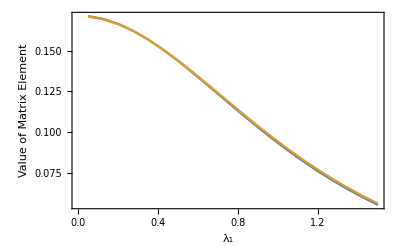

```mathematica
(* Plot <0 0 0| V | 0 0 0> with fixed λ2=.25 and varying λ1
Blue is exact, orange is Taylor approximation *)
(* I expected the error to be relatively insensitive to λ1, 
   but it seems to be just as sensitive as the λ2 dependence *)
n1=0;n=0;
l1=0;l=0;
ml1=0;ml=0;
Integrand[n1,l1,ml1,n,l,ml]; (* Initialize integrand if necessary*)
λ2=.25;b=1;
λ1min=.05;
λ1max=1.5;
Monitor[Plot[{VNonLocal[n1,l1,ml1,n,l,ml][[1,1]],VLocal[n1,l1,ml1,n,l,ml]},{λ1,λ1min,λ1max},PlotPoints->20,MaxRecursion->0,PlotRange->{{0,λ1max},All},Frame->True,FrameLabel->{"λ_1","Value of Matrix Element"}],ProgressIndicator[λ1,{λ1min,λ1max}]]
Clear[n1,n,l1,l,ml1,ml,λ1,λ2,λ2min,λ2max,b]
```

Vegas::success: Needed 280000 function evaluations.

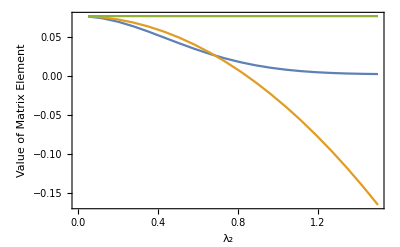

```mathematica
(* Plot <1 0 0| V | 1 0 0> with fixed λ1=1 and varying λ2
 Blue is exact, orange is Taylor approximation *)
(* In this case the exact matrix element appears to be zero,
   local approximation is still decent up until λ2~0.3 *)
n1=1;n=1;
l1=0;l=0;
ml1=0;ml=0;
Integrand[n1,l1,ml1,n,l,ml]; (* Initialize integrand if necessary*)
λ1=1;b=1;
λ2min=.05;
λ2max=1.5;
Monitor[Plot[{VNonLocal[n1,l1,ml1,n,l,ml][[1,1]],VLocal[n1,l1,ml1,n,l,ml],VLimit[n1,l1,ml1,n,l,ml]},{λ2,λ2min,λ2max},PlotPoints->20,MaxRecursion->0,PlotRange->{{0,λ2max},All},Frame->True,FrameLabel->{"λ_2","Value of Matrix Element"}],ProgressIndicator[λ2,{λ2min,λ2max}]]
Clear[n1,n,l1,l,ml1,ml,λ1,λ2,λ2min,λ2max,b]
```

Vegas::success: Needed 217000 function evaluations.

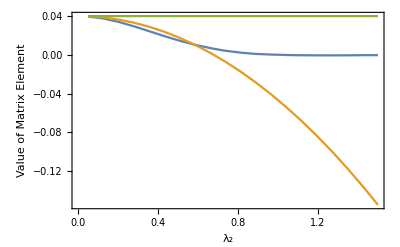

```mathematica
(* Plot <1 1 0| V | 1 1 0> with fixed λ1=1 and varying λ2
 Blue is exact, orange is Taylor approximation *)
(* In this case the exact matrix element appears to be zero,
   local approximation is still decent up until λ2~0.3 *)
n1=1;n=1;
l1=1;l=1;
ml1=0;ml=0;
Integrand[n1,l1,ml1,n,l,ml]; (* Initialize integrand if necessary*)
λ1=1;b=1;
λ2min=.05;
λ2max=1.5;
Monitor[Plot[{VNonLocal[n1,l1,ml1,n,l,ml][[1,1]],VLocal[n1,l1,ml1,n,l,ml],VLimit[n1,l1,ml1,n,l,ml]},{λ2,λ2min,λ2max},PlotPoints->20,MaxRecursion->0,PlotRange->{{0,λ2max},All},Frame->True,FrameLabel->{"λ_2","Value of Matrix Element"}],ProgressIndicator[λ2,{λ2min,λ2max}]]
Clear[n1,n,l1,l,ml1,ml,λ1,λ2,λ2min,λ2max,b]
```

Vegas::success: Needed 742000 function evaluations.

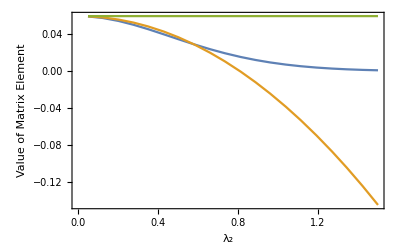

```mathematica
(* Plot <2 0 0| V | 0 0 0> with fixed λ1=1 and varying λ2
 Blue is exact, orange is Taylor approximation *)
(* In this case the exact matrix element appears to be zero,
   local approximation is still decent up until λ2~0.3 *)
n1=2;n=0;
l1=0;l=0;
ml1=0;ml=0;
Integrand[n1,l1,ml1,n,l,ml]; (* Initialize integrand if necessary*)
λ1=1;b=1;
λ2min=.05;
λ2max=1.5;
Monitor[Plot[{VNonLocal[n1,l1,ml1,n,l,ml][[1,1]],VLocal[n1,l1,ml1,n,l,ml],VLimit[n1,l1,ml1,n,l,ml]},{λ2,λ2min,λ2max},PlotPoints->20,MaxRecursion->0,PlotRange->{{0,λ2max},All},Frame->True,FrameLabel->{"λ_2","Value of Matrix Element"}],ProgressIndicator[λ2,{λ2min,λ2max}]]
Clear[n1,n,l1,l,ml1,ml,λ1,λ2,λ2min,λ2max,b]
```

Vegas::success: Needed 232000 function evaluations.

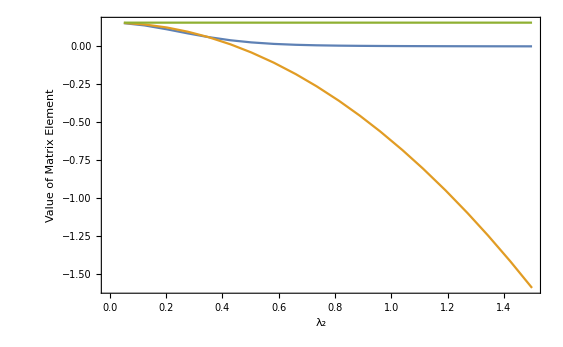

```mathematica
(* Plot <6 0 0| V | 4 0 0> with fixed λ1=0.5 and varying λ2
 Blue is exact, orange is Taylor approximation *)
(* In this case the exact matrix element appears to be zero,
   local approximation is still decent up until λ2~0.3 *)
n1=6;n=4;
l1=0;l=0;
ml1=0;ml=0;
Integrand[n1,l1,ml1,n,l,ml]; (* Initialize integrand if necessary*)
λ1=0.5;b=1;
λ2min=.05;
λ2max=1.5;
Monitor[Plot[{VNonLocal[n1,l1,ml1,n,l,ml][[1,1]],VLocal[n1,l1,ml1,n,l,ml],VLimit[n1,l1,ml1,n,l,ml]},{λ2,λ2min,λ2max},PlotPoints->20,MaxRecursion->0,PlotRange->{{0,λ2max},All},Frame->True,FrameLabel->{"λ_2","Value of Matrix Element"}],ProgressIndicator[λ2,{λ2min,λ2max}]]
Clear[n1,n,l1,l,ml1,ml,λ1,λ2,λ2min,λ2max,b]
```

Vegas::success: Needed 1957500 function evaluations.

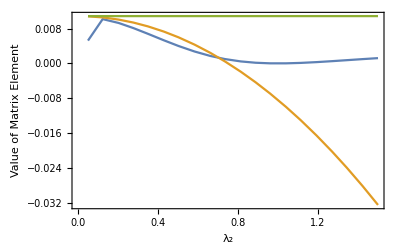

```mathematica
(* Plot <1 1 0| V | 1 1 0> with fixed λ1=1 and varying λ2
 Blue is exact, orange is Taylor approximation *)
(* In this case the exact matrix element appears to be zero,
   local approximation is still decent up until λ2~0.3 *)
n1=0;n=0;
l1=2;l=2;
ml1=0;ml=0;
Integrand[n1,l1,ml1,n,l,ml]; (* Initialize integrand if necessary*)
λ1=1;b=1;
λ2min=.05;
λ2max=1.5;
Monitor[Plot[{VNonLocal[n1,l1,ml1,n,l,ml][[1,1]],VLocal[n1,l1,ml1,n,l,ml],VLimit[n1,l1,ml1,n,l,ml]},{λ2,λ2min,λ2max},PlotPoints->20,MaxRecursion->0,PlotRange->{{0,λ2max},All},Frame->True,FrameLabel->{"λ_2","Value of Matrix Element"}],ProgressIndicator[λ2,{λ2min,λ2max}]]
Clear[n1,n,l1,l,ml1,ml,λ1,λ2,λ2min,λ2max,b]
```